# Motorbike net2 & net3

## Set Environment

```mathematica
home = "Y:/vault/h3d/";workdir = "C:/users/lichao/git/geonb/";
```

```mathematica
SetDirectory[workdir];Needs["Posecpp`","posecpp_network.wl"];
```

```mathematica
prefix = "";suffix="";
```

## Generate Network 2

### load raw data

```mathematica
rawData=LoadNetwork2Raw[home<>prefix<>"net2_raw"<>suffix<>".txt"];rawData//Dimensions
```

{233424,8}

### find best threshold

```mathematica
Module[{n = 500,v=2,a},a =ConstructNetwork2[rawData,n,v];Sow[Length[a]];
Complement[a,ConstructNetwork2[rawData,n,v-0.1]]]//Reap;
```

```mathematica
el2 = ConstructNetwork2New[rawData,50,10];g2 = Graph[el2,VertexLabels->"Name"];
```

Power::infy: Infinite expression 1/0. encountered.

Less::nord: Invalid comparison with ComplexInfinity attempted.

```mathematica
VertexCount[g2]
EdgeCount[g2]
```

518

1205

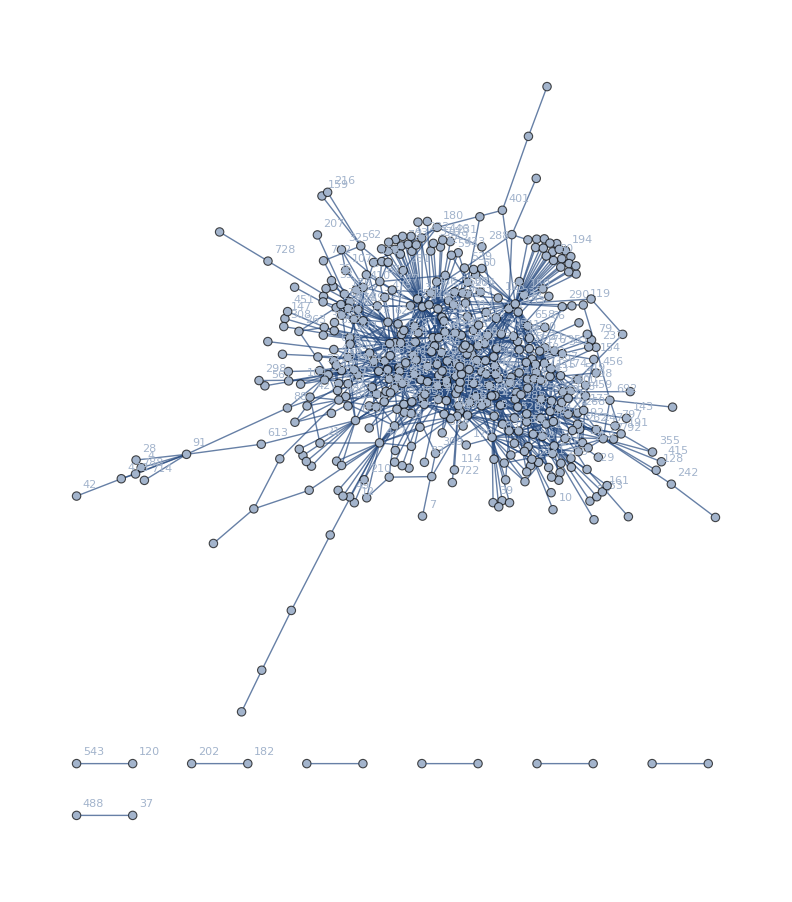

```mathematica
g2
```

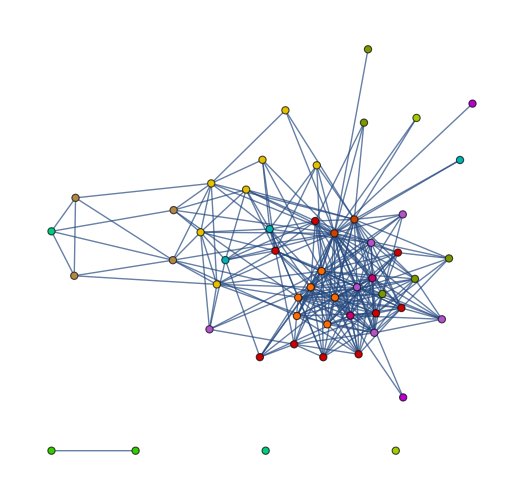

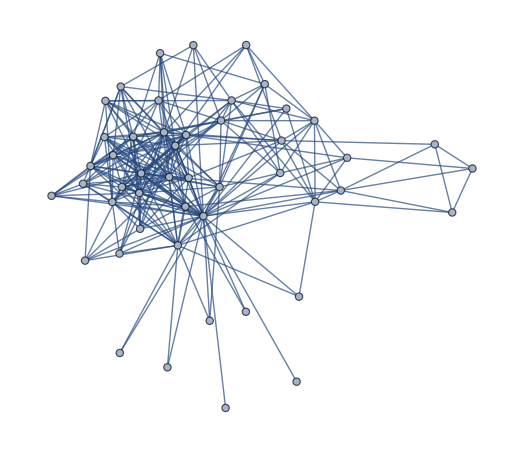

```mathematica
interGraph = Subgraph[g2,VertexList[g3]];
HighlightGraph[interGraph,comp3]
newg2= Subgraph[g2,ConnectedComponents[interGraph][[1]]]
```

```mathematica
VertexCount[newg2]
EdgeCount[newg2]
```

48

262

### Node Research

```mathematica
Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]]
```

{592,608,623,744,240,446,312,735,564,691,85,90,768,558,715,797,772,536,347,742,94,132,565,251,201,701,631,527,404,250,295,791,383,109,71,133,72,279,157,612,286,268,759,426,148,416,369,47,567,514,478,303,55,252,569,82,40,475,516,402,158,393,189,63,37,92,282,621,67,466,297,333,579,367,229,410,719,76,774,594,490,315,262,644,535,206,136,89,389,9,541,790,603,171,664,16,507,321,294,628,156,755,651,414,233,14,457,264,241,36,2,705,613,771,582,625,220,578,17,690,679,515,745,451,423,276,729,551,198,197,153,635,118,105,20,682,661,575,746,555,552,543,642,439,406,365,336,357,655,632,191,353,152,145,140,112,311,761,35,756,680,600,780,724,670,611,591,559,713,432,430,549,352,337,317,289,273,248,654,318,210,202,188,186,185,182,177,159,126,123,640,86,66,58,57,53,44,39,22}

```mathematica
HighlightGraph[NeighborhoodGraph[g2,271,VertexLabels->"Name"],VertexList[g3]]
```

### Export Graph

```mathematica
Export[home<>prefix<>"net2_el"<>suffix<>".txt",EdgeList[g2]]
```

Y:/vault/h3d/net2_el.txt